```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
sigmaCi = Interpolation[{#[[1]],{#[[2]],#[[3]]}}&/@ReadList[NotebookDirectory[]<>"sigma_CDM.dat",Table[Number,{3}]],InterpolationOrder->1];
hmfC = ReadList[NotebookDirectory[]<>"HMF_CDM.dat",Table[Number,{4}]];
hmfCi = Interpolation[{#[[1]],#[[2]],#[[3]]}&/@hmfC,InterpolationOrder->1]
dotMCi = Interpolation[{#[[1]],#[[2]],#[[4]]}&/@hmfC,InterpolationOrder->1];
```

17
InterpolatingFunction[{{0.01, 20.01}, {100000., 1. 10  }}, <>]

```mathematica
sigmaFi = Interpolation[{#[[1]],#[[2]],{#[[3]],#[[4]]}}&/@ReadList[NotebookDirectory[]<>"sigma_FDM.dat",Table[Number,{4}]],InterpolationOrder->1]
hmfF = ReadList[NotebookDirectory[]<>"HMF_FDM.dat",Table[Number,{5}]];
hmfFi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@hmfF,InterpolationOrder->1]
dotMFi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[5]]}&/@hmfF,InterpolationOrder->1];
```

17
InterpolatingFunction[{{0.8, 80.}, {100000., 1. 10  }}, <>]

17
InterpolatingFunction[{{0.8, 80.}, {0.01, 20.01}, {100000., 1. 10  }}, <>]

```mathematica
sigmaWi = Interpolation[{#[[1]],#[[2]],{#[[3]],#[[4]]}}&/@ReadList[NotebookDirectory[]<>"sigma_WDM.dat",Table[Number,{4}]],InterpolationOrder->1]
hmfW = ReadList[NotebookDirectory[]<>"HMF_WDM.dat",Table[Number,{5}]];
hmfWi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@hmfW,InterpolationOrder->1]
dotMWi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[5]]}&/@hmfW,InterpolationOrder->1];
```

```mathematica
sigmaCi[1.*^11][[1]]^2
sigmaCi[3.*^8][[1]]^2
```

9.11744

29.3391

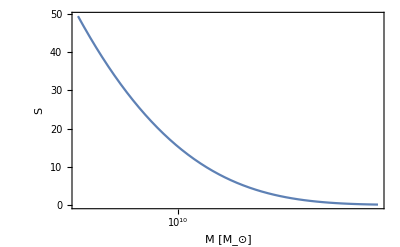

```mathematica
Plot[{sigmaCi[10^logM][[1]]^2},{logM,7,16},FrameTicks->{Automatic,{logticksx,logticksx2}},FrameLabel->{"M ["<>Msunt<>"]","S"}]
```

```mathematica
Plot[{sigmaCi[10^logM][[1]]^2,sigmaWi[3.0,10^logM][[1]]^2,sigmaFi[3.0,10^logM][[1]]^2},{logM,7,16},FrameTicks->{Automatic,{logticksx,logticksx2}},FrameLabel->{"M ["<>Msunt<>"]","S"}]
```

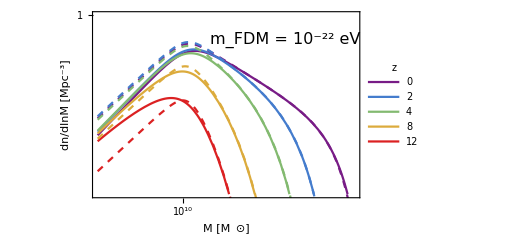

```mathematica
(* comparison with the fit of 1508.04621*)
Show[Plot[Log10[10^9hmfCi[#,10^logM](1+(10^logM/(1.6*^10 m22^(-4/3)) )^(-1.1))^(-2.2)/.m22->1.0]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,0}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,2,4,8,12},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
Plot[Log10[10^9hmfFi[1.0,#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4])],
Graphics[Text[Style["m_FDM = 10^-22 eV",16],Scaled@{0.72,0.85}]]]
```

```mathematica
(* comparison with the fit of 1308.1399 *)
αW[m3_]=49/h m3^-1.11 (Ωd/0.25)^0.11 (h/0.7)^1.22/.{h->0.674,Ωd->0.2657,ρ->39.7,μ->1.12};
TW[k_,m3_]:=(1+(αW[m3] k)^(2μ))^(-5/μ)/.{h->0.674,Ωd->0.2657,ρ->39.7,μ->1.12};
Mhm[m3_]:=4Pi/3ρ k^-3/.First@Quiet@Solve[TW[k,m3]^2==1/2,k]/.{h->0.674,Ωd->0.2657,ρ->39.7,μ->1.12}
Show[Plot[Log10[10^9hmfCi[#,10^logM](1+(3.Mhm[m3]/10^logM) )^-1.3/.m3->1.0]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,0}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,2,4,8,12},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
Plot[Log10[10^9hmfWi[1.0,#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4])],
Graphics[Text[Style["m_WDM = 1 keV",16],Scaled@{0.77,0.85}]]]
```

```mathematica
Row@{Show[Plot[Log10[10^9hmfCi[#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}}],
Plot[Log10[10^9hmfFi[1.,#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},PlotRange->{{8,16},{-9,1}},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4]),PlotPoints->100],
Graphics[Text[Style["m_FDM = 10^-22 eV",16],Scaled@{0.72,0.85}]]],Show[Plot[Log10[10^9hmfCi[#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,2,4,8,12},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
Plot[Log10[10^9hmfWi[1.0,#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},PlotRange->{{8,16},{-9,1}},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4])],
Graphics[Text[Style["m_WDM = 1 keV",16],Scaled@{0.77,0.85}]]]}
```

```mathematica
LogPlot[{10^-6*dotMCi[4,10^logM],10^-6*dotMFi[1.,4,10^logM],10^-6*dotMWi[1.,4,10^logM]},{logM,7,13},PlotRange->{All,{1.*^-2,1.*^5}},FrameLabel->{"M ["<>Msunt<>"]","dM/dt ["<>Msunt<>"/yr]"},PlotStyle->{Directive[Black,Dashed],Darker@Cyan,Orange},PlotPoints->40]
```

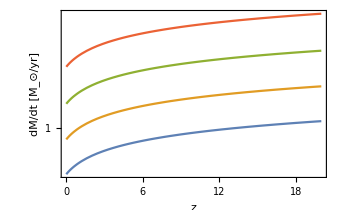

```mathematica
Plot[10^-6*dotMCi[z,10^#]&/@Range[8,14,2]//Log10//Evaluate,{z,0.01,20},FrameLabel->{"z","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340]
```

```mathematica
Plnmulist = ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]];
zlist = DeleteDuplicates[Plnmulist[[All,1]]]
Plnmulist =GatherBy[Plnmulist,First][[All,All,{2,3}]];
```

{4,5,6,7,8,9,10,11,12.5,14.5}

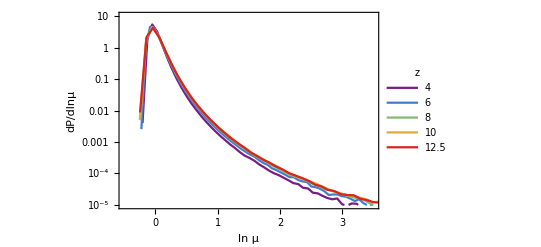

```mathematica
ListLogPlot[Plnmulist[[1;;-1;;2]],PlotRange->{{-0.5,3.5},{1.*^-5,10}},Joined->True,FrameLabel->{"ln μ","dP/dlnμ"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),PlotLegends->LineLegend[Automatic,zlist[[1;;-1;;2]],LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]]]
```

```mathematica
fB = 0.0493/0.315
```

0.156508

```mathematica
MCMCchains = Select[If[#[[-1]]=="-inf",{},Interpreter["Number"][#]]&/@StringSplit/@ReadList[NotebookDirectory[]<>"MCMCchains.dat",String],Length@#>0&];
MCMCchains[[All,1]] = MCMCchains[[All,1]]/10^11; (* Subscript[M, c] in units of 10^11 Msun *)
Length@MCMCchains
```

1708

{5.07832,0.0424352,0.907788,0.395621,1.04079,10.2731,0.219788,1304.66}

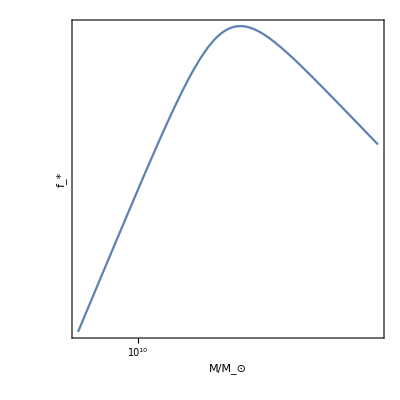
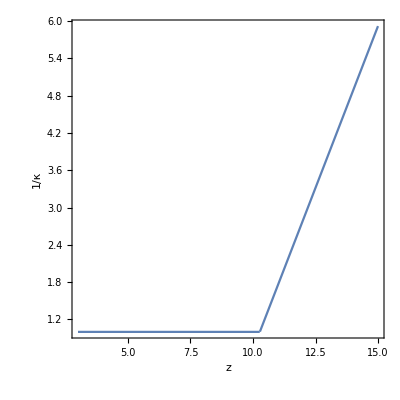
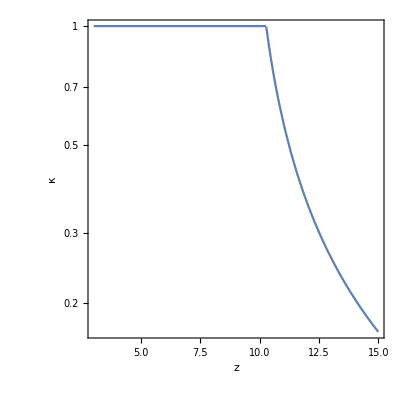

```mathematica
fstar[M_,Mc_,ϵ_,α_,β_]:=ϵ(α+β)/(β(M/Mc)^-α+α(M/Mc)^β)
First@MaximalBy[MCMCchains,Last]
Row@{Plot[Log10@fstar[10^logM,%[[1]]*10^11,%[[2]],%[[3]],%[[4]]]-Log10@fB,{logM,9,14},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotRange->{All,{All,0}},FrameLabel->{"M/"<>Msunt,"f_*"},ImageSize->{Automatic,240},ImagePadding->{{54,20},{40,10}},PlotStyle->Thick,AspectRatio->1],Plot[Max[1,1+%[[5]](z-%[[6]])],{z,3,15},FrameLabel->{"z","1/κ"},PlotRange->All,ImageSize->{Automatic,240},ImagePadding->{{54,20},{40,10}},PlotStyle->Thick,AspectRatio->1],
LogPlot[1/ Max[1,1+%[[5]](z-%[[6]])],{z,3,15},FrameLabel->{"z","κ"},PlotRange->All,ImageSize->{Automatic,240},ImagePadding->{{54,20},{40,10}},PlotStyle->Thick,AspectRatio->1]}
```

```mathematica
data1 = Import[NotebookDirectory[]<>"UVLF_2102.07775.txt","Table"];
DeleteDuplicates[data1[[All,1]]]
Φ1[z_]:=Select[data1,#[[1]]==z&][[All,2;;5]]
data2 = Import[NotebookDirectory[]<>"UVLF_2108.01090.txt","Table"];
DeleteDuplicates[data2[[All,1]]]
Φ2[z_]:=Select[data2,#[[1]]==z&][[All,2;;5]]
data3 = Import[NotebookDirectory[]<>"UVLF_2403.03171.txt","Table"];
DeleteDuplicates[data3[[All,1]]]
Φ3[z_]:=Select[data3,#[[1]]==z&][[All,2;;5]]
NPDF2[x_,μ_,σm_,σp_]:= 2Piecewise[{{σm PDF[NormalDistribution[μ,σm],x],x<μ}},σp PDF[NormalDistribution[μ,σp],x]]/(σm+σp)
```

{4,5,6,7,8,9,10}

{4,5,6,7}

{9,10,11,12.5,14.5}

```mathematica
UVL = ReadList[NotebookDirectory[]<>"UVluminosity.dat",Table[Number,{6}]];
zlist = UVL[[All,1]]//DeleteDuplicates
UVL = GatherBy[UVL,First][[All,All,2;;-1]];
UVLi = Table[Interpolation[UVL[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVL}];
```

{4,5,6,7,8,9,10,11,12.5,14.5}

```mathematica
UVLC2 = ReadList[NotebookDirectory[]<>"UVluminosityC2.dat",Table[Number,{6}]];
UVLC2 = GatherBy[UVLC2,First][[All,All,2;;-1]];
UVL2i = Table[Interpolation[UVLC2[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLC2}];
```

```mathematica
UVLW = ReadList[NotebookDirectory[]<>"UVluminosityW.dat",Table[Number,{6}]];
UVLW = GatherBy[UVLW,First][[All,All,2;;-1]];
UVLWi = Table[Interpolation[UVLW[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLW}];
```

```mathematica
UVLF = ReadList[NotebookDirectory[]<>"UVluminosityF.dat",Table[Number,{6}]];
UVLF = GatherBy[UVLF,First][[All,All,2;;-1]];
UVLFi = Table[Interpolation[UVLF[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLF}];
```

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLi[[jz]][#[[1]]],#[[2]],#[[4]],#[[3]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]]],{jz,Length@zlist}]
```

1344.42

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVL2i[[jz]][#[[1]]],#[[2]],#[[4]],#[[3]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]]],{jz,Length@zlist}]
```

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLWi[[jz]][#[[1]]],#[[2]],#[[4]],#[[3]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]]],{jz,Length@zlist}]
```

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLFi[[jz]][#[[1]]],#[[2]],#[[4]],#[[3]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]]],{jz,Length@zlist}]
```

1342.14

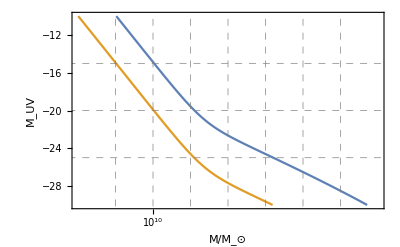

```mathematica
ListPlot[Table[{Log10@#[[2]],#[[1]]}&/@UVL[[j]],{j,{1,-1}}]//Evaluate,Joined->True,FrameLabel->{"M/"<>Msunt,"M_UV"},GridLines->{Range[9,15,1],Range[-25,-15,5]},GridLinesStyle->Directive[Gray, Dashed],PlotRange->{{8,16},{-30,-10}},FrameTicks->{Automatic,{logticksx,logticksx2}}]
```

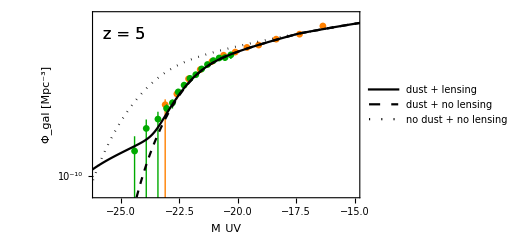

```mathematica
jz0 = 2;
Legended[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Orange,PlotRange->{{-26,-15},{-11,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->380],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.12,0.88}]],
ListPlot[{{#[[1]],Log10[10^9#[[3]]]}&/@UVL[[jz0]],{#[[1]],Log10[10^9#[[4]]]}&/@UVL[[jz0]],{#[[1]],Log10[10^9#[[5]]]}&/@UVL[[jz0]]}//Evaluate,PlotRange->{{-30,-15},{-12,-1}},Joined->True,PlotStyle->{Directive[Black,Dotted],Directive[Black,Dashed],Black}],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.12,0.88}]]],Placed[LineLegend[{Black,Directive[Black,Dashed],Directive[Black,Dotted]},{"dust + lensing","dust + no lensing","no dust + no lensing"},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendMarkerSize->{24,4}],Scaled@{0.72,0.25}]]
```

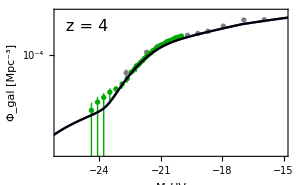
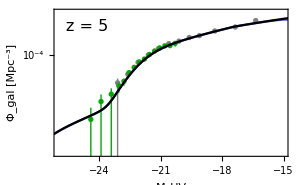
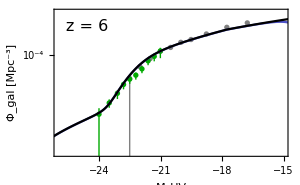
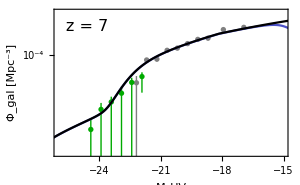
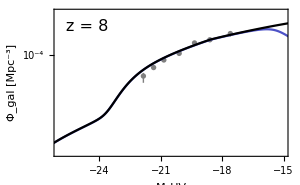
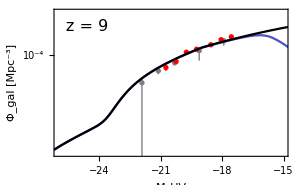
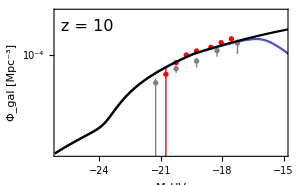
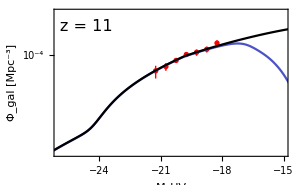
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
Grid@ArrayReshape[Table[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Gray,PlotRange->{{-26,-15},{-11,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->300],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Red],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLF[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[RGBColor[0.3,0.32,0.78]]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVL[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Black]],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.14,0.88}]]],{jz0,Length@zlist}],{3,4}]
```

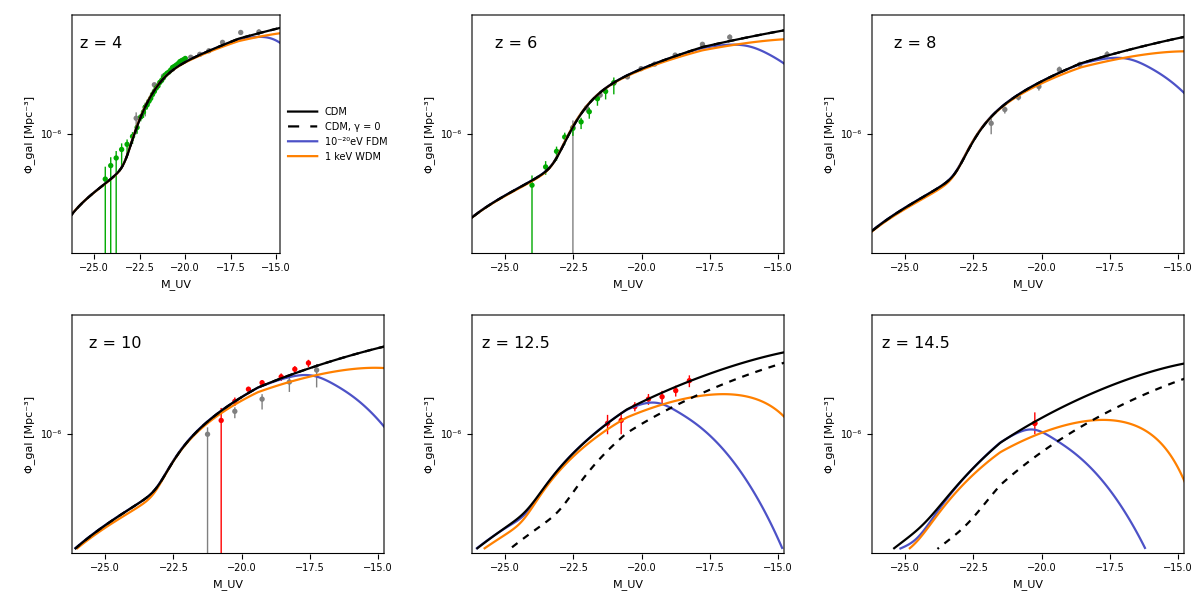

```mathematica
Legended[Grid@ArrayReshape[Table[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Gray,PlotRange->{{-26,-15},{-11,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->300],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Red],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLF[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[RGBColor[0.3,0.32,0.78]]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLW[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Orange]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVL[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Black]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLC2[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Black,Dashed]],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.14,0.88}]]],{jz0,{1,3,5,7,9,10}}],{2,3}],Placed[LineLegend[{Black,Directive[Black,Dashed],RGBColor[0.3,0.32,0.78],Orange},{"CDM","CDM, γ = 0","10^-20eV FDM","1 keV WDM"},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendMarkerSize->{20,20}],Right]]
```

```mathematica
Mlist = ReadList[NotebookDirectory[]<>"BHmassStellarmass.dat",Table[Number,{4}]];
```

```mathematica
Mlist[[All,1]]//DeleteDuplicates
```

{0.01,0.0107981,0.0116598,0.0125903,0.0135951,0.0146801,0.0158517,0.0171168,0.0184828,0.0199578,0.0215506,0.0232705,0.0251276,0.027133,0.0292983,0.0316365,0.0341613,0.0368876,0.0398315,0.0430103,0.0464428,0.0501493,0.0541515,0.0584731,0.0631397,0.0681786,0.0736197,0.0794951,0.0858393,0.0926898,0.100087,0.108075,0.1167,0.126013,0.13607,0.146929,0.158655,0.171317,0.184989,0.199752,0.215694,0.232907,0.251495,0.271566,0.293238,0.316641,0.341911,0.369197,0.398662,0.430478,0.464833,0.501929,0.541986,0.58524,0.631946,0.68238,0.736838,0.795643,0.85914,0.927705,1.00174,1.08169,1.16801,1.26123,1.36188,1.47057,1.58793,1.71466,1.8515,1.99926,2.15881,2.3311,2.51714,2.71802,2.93494,3.16916,3.42208,3.69519,3.99009,4.30852,4.65237,5.02366,5.42458,5.8575,6.32497,6.82974,7.3748,7.96335,8.59888,9.28513,10.0261,10.8263,11.6903,12.6233,13.6307,14.7185,15.8931,17.1615,18.5311,20.01}

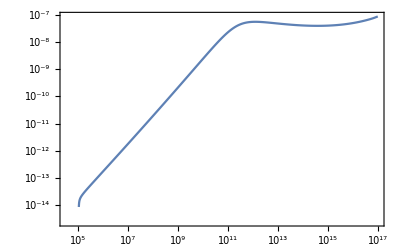

```mathematica
ListLogLogPlot[{#[[2]],#[[4]]/#[[2]]}&/@Select[Mlist,#[[1]]==0.01&],Joined->True]
```

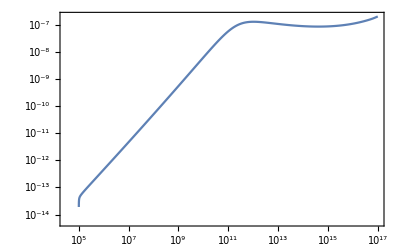

```mathematica
ListLogLogPlot[{#[[2]],#[[4]]/#[[2]]}&/@Select[Mlist,#[[1]]==0.01&],Joined->True]
```

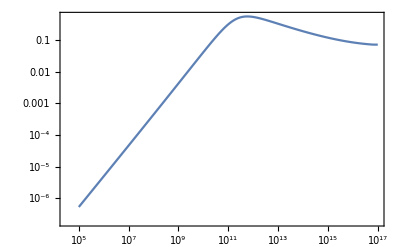

```mathematica
ListLogLogPlot[{#[[2]],#[[4]]/#[[2]]}&/@Select[Mlist,#[[1]]==0.01&],Joined->True]
```